```mathematica
(* Fijar directorio a mis archivos dentro del repositorio *)
SetDirectory[NotebookDirectory[]];

(* Cargar paquetes *)
Get["../Mathematica_packages/QMB.wl"];
```

```mathematica
LaunchKernels[]
```

{Local,Local}

```mathematica
hx=J=1.;
hz=0.5;

times={};
```

### Time

```mathematica
Do[

AppendTo[times,AbsoluteTiming[
(* Calcular los índices de las Pauli strings en la suma del valor esperado de Haar de la pureza de Choi *)
indices = Tuples[Range[0, 3], L - 1];

(* Crear Hamiltoniano *)
H=IsingNNOpenHamiltonian[hx, hz, J, L];

(* Diagonalizar H *)
{eigenvalues, eigenvectors}=Chop[Eigensystem[H]];

(* Calcular la matriz de cambio de base de la de eigenenergías a computacional *)
P = Transpose[eigenvectors];

(* Calcular operador de evolución *)
ClearAll[U];
U[t_] := P . DiagonalMatrix[Exp[-I*eigenvalues*t]] . ConjugateTranspose[P];

(* Calcular promedio de Haar de la pureza de Choi promedio cuando los estados iniciales del entorno son aleatorios producto *)
haarAvgOfChoiPurity = 
ParallelTable[
	u = U[t];{t, Chop[Total[(1/2)^2*(1/12)^(L-1)*Purity[MatrixPartialTrace[u . (Sqrt[Power[3,(L-1)-Count[#,x_/;x!=0]]]*Pauli[Join[{0},#]]) . ConjugateTranspose[u], 1, 2]] &/@ indices]]}
	,{t, 0., 100., 0.5}
, DistributedContexts -> Full];

(* Calcular el promedio temporal del promedio de Haar de la pureza de Choi de 0s a 100s *)
fInterp = Interpolation[haarAvgOfChoiPurity]; 
timeAvgOfHaarAvgOfChoiPurity = NIntegrate[fInterp[t],{t, 0, 100}] / 100.;
][[1]]];

,{L,8,8}]
```

$Aborted

```mathematica
times
```

{0.319748,0.811059,2.95527,13.5879,92.7859}

```mathematica
data=Transpose[{Range[3,7],times}]
```

{{3,0.319748},{4,0.811059},{5,2.95527},{6,13.5879},{7,92.7859}}

{a→0.000156364,b→1.89905}

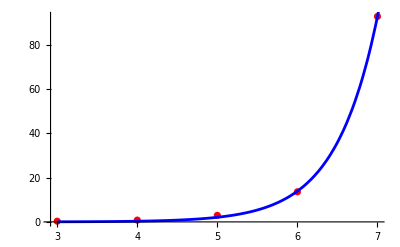

```mathematica
fit=FindFit[data,a Exp[b x],{a,b},x]
Show[ListPlot[data,PlotStyle->Red],Plot[a Exp[b x]/. fit,{x,3,8},PlotStyle->Blue]]
```

```mathematica
data=Transpose[{Range[3,7],times/3600.}]
```

{{3,0.0000888189},{4,0.000225294},{5,0.000820909},{6,0.00377441},{7,0.0257739}}

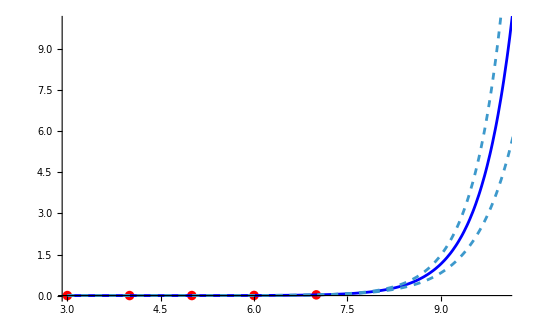

```mathematica
Show[ListPlot[data,PlotStyle->Red](*Plot the data points in red*),
Plot[model[x]/3600,{x,3,12},PlotStyle->Blue](*Plot the fitted curve in blue*),
Plot[model["MeanPredictionBands"]/3600/. x->x,{x,3,12},PlotStyle->Dashed] (*Confidence bands as dashed lines*),
PlotRange->{{3,10},{0,10}}
]
```

```mathematica
model[8]/60.
```

10.3269

```mathematica
(model["MeanPredictionBands"]/.x->8)/60
```

{8.84156,11.8122}

### Memory

```mathematica
memory={};
```

```mathematica
Do[

AppendTo[memory,MaxMemoryUsed[
(* Calcular los índices de las Pauli strings en la suma del valor esperado de Haar de la pureza de Choi *)
indices = Tuples[Range[0, 3], L - 1];

(* Crear Hamiltoniano *)
H=IsingNNOpenHamiltonian[hx, hz, J, L];

(* Diagonalizar H *)
{eigenvalues, eigenvectors}=Chop[Eigensystem[H]];

(* Calcular la matriz de cambio de base de la de eigenenergías a computacional *)
P = Transpose[eigenvectors];

(* Calcular operador de evolución *)
ClearAll[U];
U[t_] := P . DiagonalMatrix[Exp[-I*eigenvalues*t]] . ConjugateTranspose[P];

(* Calcular promedio de Haar de la pureza de Choi promedio cuando los estados iniciales del entorno son aleatorios producto *)
haarAvgOfChoiPurity = 
ParallelTable[
	u = U[t];{t, Chop[Total[(1/2)^2*(1/12)^(L-1)*Purity[MatrixPartialTrace[u . (Sqrt[Power[3,(L-1)-Count[#,x_/;x!=0]]]*Pauli[Join[{0},#]]) . ConjugateTranspose[u], 1, 2]] &/@ indices]]}
	,{t, 0., 100., 0.5}
, DistributedContexts -> Full];

(* Calcular el promedio temporal del promedio de Haar de la pureza de Choi de 0s a 100s *)
fInterp = Interpolation[haarAvgOfChoiPurity]; 
timeAvgOfHaarAvgOfChoiPurity = NIntegrate[fInterp[t],{t, 0, 100}] / 100.;
]];

,{L,3,7}]
```

```mathematica
Table[indices = Tuples[Range[0, 3], L - 1];ByteCount[Pauli[Join[{0},#]]&/@indices]/10.^9,{L,3,8}]
```

{0.000014568,0.00008544,0.000563232,0.00403091,0.0305396,0.238938}

```mathematica
Table[indices = Tuples[Range[0, 3], L - 1];ByteCount[Normal@Pauli[Join[{0},#]]&/@indices]/10.^9,{L,3,6}]
```

{0.000021424,0.000323504,0.00501747,0.0789623}

```mathematica
0.23893793600000002*8*8
```

15.292

```mathematica
hx=J=1.;
hz=0.5;
L=6;indices = Tuples[Range[0, 3], L - 1];

(* Crear Hamiltoniano *)
H=IsingNNOpenHamiltonian[hx, hz, J, L];

(* Diagonalizar H *)
{eigenvalues, eigenvectors}=Chop[Eigensystem[H]];

(* Calcular la matriz de cambio de base de la de eigenenergías a computacional *)
P = Transpose[eigenvectors];

(* Calcular operador de evolución *)
ClearAll[U];
U[t_] := P . DiagonalMatrix[Exp[-I*eigenvalues*t]] . ConjugateTranspose[P];
```

```mathematica
t=1.4;
u = U[t];
AbsoluteTiming[{t, Chop[Total[(1/2)^2*(1/12)^(L-1)*Purity[MatrixPartialTrace[u . (Sqrt[Power[3,(L-1)-Count[#,x_/;x!=0]]]*Pauli[Join[{0},#]]) . ConjugateTranspose[u], 1, 2]] &/@ indices]]}]

AbsoluteTiming[{t, Chop[Total[(1/2)^2*(1/12)^(L-1)*Purity[MatrixPartialTrace[u . (Sqrt[Power[3,(L-1)-Count[#,x_/;x!=0]]]*Pauli[Join[{0},#]]) . ConjugateTranspose[u], 1, 2]] &/@ indices]]}]

paulis=Pauli[Join[{0},#]]&/@indices;
AbsoluteTiming[{t, Chop[Total[(1/2)^2*(1/12)^(L-1)*ParallelSum[Purity[MatrixPartialTrace[u . (Sqrt[Power[3,(L-1)-Count[indices[[i]],x_/;x!=0]]]*paulis[[i]]) . ConjugateTranspose[u], 1, 2]] ,{i,4^(L-1)}]]]}]

paulis=Normal[Pauli[Join[{0},#]]&/@indices];
AbsoluteTiming[{t, Chop[Total[(1/2)^2*(1/12)^(L-1)*ParallelSum[Purity[MatrixPartialTrace[u . (Sqrt[Power[3,(L-1)-Count[indices[[i]],x_/;x!=0]]]*paulis[[i]]) . ConjugateTranspose[u], 1, 2]] ,{i,4^(L-1)}]]]}]
```

{0.836759,{1.4,0.436099}}

{2.63344,{1.4,0.436099}}

{11.4791,{1.4,0.436099}}